# General Polyhedron -Graphics- |z_1⟩ =|z_1⟩ |ω_1⟩ =|ω_1⟩ |z_2⟩ = |z_2⟩ |ω_2⟩ = |ω_2⟩ ... ... |z_(N-1)⟩ = |z_(N-1)⟩ |ω_(N-1)⟩ = |ω_(N-1)⟩ |z_N⟩ = |z_N⟩ |ω_N⟩ =|ω_N⟩

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

```mathematica
messageHandler=If[Last[#],Interrupt[]]&;
Internal`AddHandler["Message",messageHandler];
```

## Main

```mathematica
evolution[parameters_]:=Module[{array=parameters},
{γ,H0,λ}={array[["γ"]], array[["H0"]],array[["λ"]]};
{tmin,tmax}={array[["tmin"]],array[["tmax"]]};
 {n}={array[["edges"]]};
{ndsolvemethod}={array[["method"]]};

{z,ω}={List[],List[]};
For[i=1,i≤ n,i++,
z=Append[z,{Symbol["z"<>ToString@i<>ToString@1],Symbol["z"<>ToString@i<>ToString@2]}];
ω=Append[ω,{Symbol["ω"<>ToString@i<>ToString@1],Symbol["ω"<>ToString@i<>ToString@2]}]];

Matrices;
Eα[t_]=Table[z[[i,1]][t]* z[[j,1]][t]+z[[i,2]][t]* z[[j,2]][t],{i,1,n},{j,1,n}];
Fα[t_]=Table[-z[[j,1]][t] z[[i,2]][t]+z[[j,2]][t]z[[i,1]][t],{i,1,n},{j,1,n}];
Fcα[t_]=Fα[t]*;
Eβ[t_]=Table[ω[[i,1]][t]* ω[[j,1]][t]+ω[[i,2]][t]* ω[[j,2]][t],{i,1,n},{j,1,n}];
Fβ[t_]=Table[-ω[[j,1]][t] ω[[i,2]][t]+ω[[j,2]][t]ω[[i,1]][t],{i,1,n},{j,1,n}];
Fcβ[t_]=Fβ[t]*;

Solve differential equations;
{eqz0,eqz1,eqω0,eqω1}={List[],List[],List[],List[]};
{soluz0,soluz1,soluω0,soluω1}={List[],List[],List[],List[]};
For[i=1,i≤ n,i++,
		eqz0=Append[eqz0,z[[i,1]]'[t]==Sum[-ⅈ λ[[i,l]] Eβ[t][[i,l]] z[[l,1]][t]-2 ⅈ γ[[i,l]]* Fcβ[t][[i,l]]z[[l,2]][t]*,{l,1,n}]];
		eqz1=Append[eqz1,z[[i,2]]'[t]==Sum[-ⅈ λ[[i,l]] Eβ[t][[i,l]] z[[l,2]][t]+2 ⅈ γ[[i,l]]* Fcβ[t][[i,l]]z[[l,1]][t]*,{l,1,n}]];
		eqω0=Append[eqω0,ω[[i,1]]'[t]==Sum[-ⅈ λ[[i,l]] Eα[t][[i,l]] ω[[l,1]][t]-2 ⅈ γ[[i,l]]* Fcα[t][[i,l]]ω[[l,2]][t]*,{l,1,n}]];
		eqω1=Append[eqω1,ω[[i,2]]'[t]==Sum[-ⅈ λ[[i,l]] Eα[t][[i,l]] ω[[l,2]][t]+2 ⅈ γ[[i,l]]* Fcα[t][[i,l]]ω[[l,1]][t]*,{l,1,n}]]];

z0vec=Table[z[[i,1]][0]==z0[[i,1]],{i,1,n}];
z1vec=Table[z[[i,2]][0]==z0[[i,2]],{i,1,n}];
ω0vec=Table[ω[[i,1]][0]==ω0[[i,1]],{i,1,n}];
ω1vec=Table[ω[[i,2]][0]==ω0[[i,2]],{i,1,n}];
initialconditions=Join[z0vec,z1vec,ω0vec, ω1vec];

For[i=1,i≤n,i++,
times={};
soluz0=Append[soluz0,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, z[[i,1]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluz1=Append[soluz1,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, z[[i,2]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluω0=Append[soluω0,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, ω[[i,1]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluω1=Append[soluω1,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, ω[[i,2]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",StepMonitor:>AppendTo[times,t],PrecisionGoal-> ∞]];
];

times = Sort[times];
times = Range[tmin, tmax, (tmax-tmin)/500];

solutions=Flatten[{soluz0,soluz1,soluω0,soluω1}];

Hamiltonian;
e[t_]= ∑_(i=1)^n (∑_(j=1)^n λ[[i,j]]Eα[t][[i,j]]Eβ[t][[i,j]]);
f[t_]=  ∑_(i=1)^n (∑_(j=1)^n γ[[i,j]] Fα[t][[i,j]]Fβ[t][[i,j]]);
fc[t_]=∑_(i=1)^n (∑_(j=1)^n γ[[i,j]]*Fcα[t][[i,j]]Fcβ[t][[i,j]]);
H[t_]= e[t]+f[t]+fc[t];

Closure Constraint;
closurez1[t_]=Sum[Abs[z[[i,1]][t]]^2-Abs[z[[i,2]][t]]^2,{i,1,n}];
closurez2[t_]=Sum[z[[i,1]][t] z[[i,2]][t]*,{i,1,n}];
closureω1[t_]=Sum[Abs[ω[[i,1]][t]]^2-Abs[ω[[i,2]][t]]^2,{i,1,n}];
closureω2[t_]=Sum[ω[[i,1]][t] ω[[i,2]][t]*,{i,1,n}];

Quadrupole;
σ[1]={{0,1},{1,0}};
σ[2]={{0,-ⅈ},{ⅈ,0}};
σ[3]={{1,0},{0,-1}};

zz[t_]=List[];
For[i=1,i≤ n,i++,
	zz[t_]=Append[zz[t],{z[[i,1]][t],z[[i,2]][t]}]];

quadrupole[t_,a_,b_]=1/2 Sum[((zz[t][[k]]*.σ[a].zz[t][[k]]) (zz[t][[k]]*.σ[b]. zz[t][[k]]))/(zz[t][[k]]*.zz[t][[k]]),{k,n}];

T[t_]={{quadrupole[t,1,1],quadrupole[t,1,2],quadrupole[t,1,3]},
	     {quadrupole[t,2,1],quadrupole[t,2,2],quadrupole[t,2,3]},
	     {quadrupole[t,3,1],quadrupole[t,3,2],quadrupole[t,3,3]}};

MaximumT={{NMaximize[{Evaluate[quadrupole[t,1,1]/.solutions],tmin<t<tmax},t][[1]],
		  NMaximize[{Evaluate[quadrupole[t,1,2]/.solutions],tmin<t<tmax},t][[1]],
		  NMaximize[{Evaluate[quadrupole[t,1,3]/.solutions],tmin<t<tmax},t][[1]]},
		 {NMaximize[{Evaluate[quadrupole[t,2,1]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,2,2]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,2,3]/.solutions],tmin<t<tmax},t][[1]]},
		 {NMaximize[{Evaluate[quadrupole[t,3,1]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,3,2]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,3,3]/.solutions],tmin<t<tmax},t][[1]]}};
maxquad=Re[Max[MaximumT]];

area[t_]=Re[quadrupole[t,1,1]+quadrupole[t,2,2]+quadrupole[t,3,3]];

{a0[t_],b0[t_],c0[t_]}={quadrupole[t,1,1],quadrupole[t,2,2],quadrupole[t,1,2]};

eigenvalues[t_]=Re[{1/2((a0[t]+b0[t])+Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      1/2((a0[t]+b0[t])-Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      quadrupole[t,3,3]}/.solutions];
eigenvectors[t_]={Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[1]]),0}],
				Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[2]]),0}],
				{0,0,1}}/.solutions;

Volume;
SetDirectory[NotebookDirectory[]];

nor[t_,a_]:={zz[t][[a]]*.σ[1].zz[t][[a]],zz[t][[a]]*.σ[2].zz[t][[a]],zz[t][[a]]*.σ[3].zz[t][[a]]};

volume = {};
For[tstep=1, tstep≤ Length[times], tstep++,

normals ={};
For[i=1, i≤ n, i++,
normals = Append[normals, Re[nor[times[[tstep]],i]/.solutions]]];

Export["normals.txt",ExportString[Flatten[Re[normals]],"PythonExpression"]];
RunProcess[{"Python", "reconstruction.py"}];

vertices = Import["vertices.csv","CSV"];
faces =  DeleteCases[IntegerPart[Import["faces.csv","CSV"]],0,2];
volume = Append[volume,{times[[tstep]],Import["volume.csv", "CSV"][[1,1]]}];

Run["rm vertices.csv"];
Run["rm faces.csv"];
Run["rm volume.csv"];
poli = Graphics3D[{Magenta, Opacity[.7],Polyhedron[vertices,faces]},Boxed->False];
Export["pics/"<> IntegerString[tstep,10,4]<>".png",poli,ImageResolution->200];


];

(*Plots;

Spinors;
plotz=Join[Table[Abs[z[[i,1]][t]/.solutions],{i,1,n}],
		    Table[Abs[z[[i,2]][t]/.solutions],{i,1,n}]];
zlabel=Join[Table[MaTeX["|z_{"<>ToString@i<>"1}|"],{i,1,n}],
		      Table[MaTeX["|z_{"<>ToString@i<>"2}|"],{i,1,n}]];
plotω=Join[Table[Abs[ω[[i,1]][t]/.solutions],{i,1,n}],
		    Table[Abs[ω[[i,2]][t]/.solutions],{i,1,n}]];
ωlabel=Join[Table[MaTeX["|\\omega_{"<>ToString@i<>"1}|"],{i,1,n}],
		      Table[MaTeX["|\\omega_{"<>ToString@i<>"2}|"],{i,1,n}]];

gr1 =Plot[{plotz}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None}, AxesOrigin-> {0,0},PlotLegends-> Placed[{zlabel}, Above],PlotStyle -> {Thickness[0.004],Dashed}];
gr11 =Plot[{plotω}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[{ωlabel}, Above],PlotStyle -> {Thickness[0.004],Dashed}];

Area;
totalareaz=1/2 Sum[Abs[z[[i,1]][t]/.solutions]^2+Abs[z[[i,2]][t]/.solutions]^2,{i,1,n}];
individualareaz=1/2 Table[Abs[z[[i,1]][t]/.solutions]^2+Abs[z[[i,2]][t]/.solutions]^2,{i,1,n}];
labelareaz=Table[MaTeX["X_"<>ToString@i],{i,1,n}];
totalareaω=1/2 Sum[Abs[ω[[i,1]][t]/.solutions]^2+Abs[ω[[i,2]][t]/.solutions]^2,{i,1,n}];
individualareaω=1/2 Table[Abs[ω[[i,1]][t]/.solutions]^2+Abs[ω[[i,2]][t]/.solutions]^2,{i,1,n}];
labelareaω=Table[MaTeX["Y_"<>ToString@i],{i,1,n}];

gr2 = Plot[{totalareaz,individualareaz}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[Flatten[{MaTeX["\\sum_{i} X_{i}"],labelareaz}],Above],PlotRange-> All];
gr12 = Plot[{totalareaω,individualareaω}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[Flatten[{MaTeX["\\sum_{i} Y_{i}"],labelareaω}],Above],PlotRange-> All];

Closure;
gr3 = Plot[{Abs[closurez1[t]/.solutions],
		 Abs[closurez2[t]/.solutions],
		 Abs[closureω1[t]/.solutions],
		 Abs[closureω2[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\text{Closure1 }z"],MaTeX["\\text{Closure2 }z"],
																			MaTeX["\\text{Closure1 }\\omega"],MaTeX["\\text{Closure2 }\\omega"]}, Above],PlotRange-> {-0.01,0.01},AxesLabel-> {MaTeX["t"],None}, PlotStyle -> {Blue,Darker[Green], Directive[Red,Dashed],Directive[Brown,Dashed]}];

Hamiltonian;
gr4= Plot[{Re[e[t]/.solutions],
		Im[e[t]/.solutions],
		Abs[e[t]/.solutions]},{t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(e)"], MaTeX["\\operatorname{Im}(e)"], MaTeX["\\operatorname{Abs}(e)"]},Above],
												 PlotStyle -> {Blue, Red,  Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr5=Plot[{Re[f[t]/.solutions],
		Im[f[t]/.solutions],
		Abs[f[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f)"], MaTeX["\\operatorname{Im}(f)"], MaTeX["\\operatorname{Abs}(f)"]},Above],
														  PlotStyle -> {Blue, Red,  Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr6=Plot[{Re[fc[t]/.solutions],
		Im[fc[t]/.solutions],
		Abs[fc[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f^{*})"],MaTeX["\\operatorname{Im}(f^{*})"], MaTeX["\\operatorname{Abs}(f^{*})"]},Above],
															PlotStyle -> {Blue, Red, Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr7=Plot[{Re[H[t]/.solutions],
		Im[H[t]/.solutions],
		Abs[H[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(H)"], MaTeX["\\operatorname{Im}(H)"], MaTeX["\\operatorname{Abs}(H)"]},Above],
														PlotRange-> All,PlotStyle -> {Blue, Red, Darker[Green]},AxesLabel-> {MaTeX["t"],None}];

Quadrupole;
gr8 = Show[GraphicsGrid[Table[Plot[Abs[quadrupole[t,i,j]/.solutions],{t,tmin,tmax},PlotRange-> {0,maxquad},AxesLabel-> {MaTeX["t"],None}],{i,3},{j,3}]],PlotLabel->MaTeX["\\text{Quadrupole}"]];
gr9 = Plot[{totalareaz,totalareaω,area[t]/.solutions},{t,tmin,tmax},AxesOrigin-> {0,0},PlotLegends-> Placed[{MaTeX["E_z"],MaTeX["E_\\omega"], MaTeX["\\operatorname{Tr}[Q]"]},Above],PlotRange-> All,PlotStyle -> {Blue, Directive[Darker[Green],Dashed],Directive[Red,Dotted]},AxesLabel-> {MaTeX["t"],None}];
gr10=Plot[{eigenvalues[t][[1]],eigenvalues[t][[2]],eigenvalues[t][[3]]},{t,tmin,tmax},AxesOrigin-> {0,0},PlotStyle -> {Darker[Green],Blue, Red},
	PlotLegends-> Placed[{MaTeX["Q_{1}"], MaTeX["Q_{2}"],MaTeX["Q_{3}"]},Above],AxesLabel-> {MaTeX["t"],None}];*)

Volume;
gr13=ListLinePlot[{volume},PlotRange-> {0,All},PlotLabel->MaTeX["\\text{Volume}"],AxesLabel-> {MaTeX["t"],None}];

Return;
<|(*"spinorsz"-> gr1,"Ez"-> gr2,"closure"-> gr3 ,"e"-> gr4, "f"-> gr5, "fc"-> gr6, "H"-> gr7,
  "quad"-> gr8, "checkareas"-> gr9,"eigenvalues"-> gr10,"spinorsω"-> gr11,"Eω"-> gr12, *)"volume"-> gr13|>
];
```

## Build Initial System

```mathematica
initialvalues[parameters_]:=Module[{array=parameters},
{γ,H0,λ}={array[["γ"]], array[["H0"]],array[["λ"]]};
 {n}={array[["edges"]]};
{ndsolvemethod,save}={array[["method"]],array[["save"]]};

SeedRandom[Method -> "MersenneTwister"];
	points = {};
	For[i = 1, i≤ n , i++,
	u = RandomReal[{0, 1}];
	v = RandomReal[{0, 1}];
	θ= 2 π u;
	ϕ = ArcCos[2 v-1];
	points=Append[points,{Sin[ϕ] Cos[θ],Sin[ϕ] Sin[θ],Cos[ϕ]}]];

weight=RandomVariate[NormalDistribution[0,1/Sqrt[2]],n];
For[i=1,i≤ n,i++,
points[[i]] = points[[i]] weight[[i]]];

z0={};
For [i=1,i≤ n,i++,
phase=ArcTan[points[[i,2]]/points[[i,1]]];
z0=Append[z0,{ Sqrt[(Norm[points[[i]]]+points[[i,3]])/2],ⅇ^(-ⅈ phase) Sqrt[(Norm[points[[i]]]-points[[i,3]])/2]}]];

X11=Sum[Abs[z0[[i,1]]]^2,{i,1,n}];
X12=Sum[z0[[i,1]] z0[[i,2]]*,{i,1,n}];
X22=Sum[Abs[z0[[i,2]]]^2,{i,1,n}];

randomchoice=RandomInteger[{1,4}];
 Λcomp=NSolve[{X11==(X11 X22 -X12 X12*)(α α* + β β*),
		      X12==(X11 X22 -X12 X12*) (α η* + β δ*),
		      X12*==(X11 X22 -X12 X12*) (α* η + β* δ),
		      X22==(X11 X22 -X12 X12*)(η η*+ δ δ*),
		      α==α*,
		      β==η*,
		      β*==η,
		      δ==δ*},{α,β,η,δ,α*,β*,η*,δ*},Complexes][[randomchoice]];

Λ={{Λcomp[[1,2]],Λcomp[[2,2]]},
     {Λcomp[[3,2]],Λcomp[[4,2]]}};

For [i=1,i≤n,i++,
	z0[[i]]=Inverse[Λ].z0[[i]]];

randomizedlabels=RandomSample[Range[1,n]];

eq1=zi0'[t]==-ⅈ (zj0[t]* zi0[t] + zj1[t]* zi1[t]) zj0[t];
eq2=zi1'[t]==-ⅈ (zj0[t]* zi0[t] + zj1[t]* zi1[t]) zj1[t];
eq3=zj0'[t]==-ⅈ (zi0[t]* zj0[t] + zi1[t]* zj1[t]) zi0[t];
eq4=zj1'[t]==-ⅈ (zi0[t]* zj0[t] + zi1[t]* zj1[t]) zi1[t];

ω0=z0;
For[i=1,i≤ n,i++,
	If[i≠n,j=i+1,j=1];

	randomtime=RandomReal[{0,100}];
	{coordi,coordj}={randomizedlabels[[i]],randomizedlabels[[j]]};

	initialspinors={zi0[0]==ω0[[coordi,1]], zi1[0]==ω0[[coordi,2]], zj0[0]== ω0[[coordj,1]], zj1[0]==ω0[[coordj,2]]};
	soluzi0=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zi0,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzi1=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zi1,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzj0=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zj0,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzj1=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zj1,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	solutions0=Flatten[{soluzi0,soluzi1,soluzj0,soluzj1}];

	ω0[[coordi,1]]=zi0[randomtime]/.solutions0;
	ω0[[coordi,2]]=zi1[randomtime]/.solutions0;
	ω0[[coordj,1]]=zj0[randomtime]/.solutions0;
	ω0[[coordj,2]]=zj1[randomtime]/.solutions0;

	Clear[zi0,zi1,zj0,zj1,soluzi0,soluzi1,soluzj0,soluzj1,solutions0]];


If[save=="Yes",
today=Now;
folder=DateString[today,{"Day","-","Month","-","Year"}];
file=DateString[today,{"Hour",".", "Minute",".","Second"}];
location="/Users/enekoaranguren/Documents/lqg/plots/";
foldername=location<>folder<>"/";
filename=foldername<>file<>".mx";

initialdata=<|"edges"-> n,"H0"-> H0,"γ"-> γ,"λ"-> λ,"z0"-> z0,"ω0"-> ω0|>;

With[{dirname=foldername},
	Switch[FileType[dirname],
			None,CreateDirectory[dirname]]];
Export[filename,initialdata],None];
Print[filename];
<|"z0"-> z0, "ω0"-> ω0,"Λ"-> Λ|>
];
```

## Print Plots

```mathematica
plot[parameters_]:=Module[{array=parameters},
params=array;

location="/Users/enekoaranguren/Documents/lqg/plots/";

If[ToString[params[["initialdata"]]]=="None",
ini=initialvalues[params];
{params[["z0"]],params[["ω0"]]}={ini[["z0"]],ini[["ω0"]]},

ini=Import[location<>params[["initialdata"]]<>".mx"];
{z0,ω0}={ini[["z0"]],ini[["ω0"]]};
{params[["λ"]],params[["γ"]],params[["edges"]],params[["H0"]]}={ini[["λ"]],ini[["γ"]] ,ini[["edges"]],ini[["H0"]]}];

allplots=evolution[params];

Print[MaTeX["\\text{\\Huge{Spinors}}"]];
Print[""];
Print[Style[Row[{allplots[["spinorsz"]],allplots[["Ez"]],allplots[["spinorsω"]],allplots[["Eω"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{\\Huge{Quadrupole and Volume}}"]];
Print[""];
Print[Style[Row[{allplots[["quad"]],allplots[["eigenvalues"]],allplots[["volume"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{\\Huge{Consistency Checks}}"]];
Print[Style[Row[{allplots[["closure"]],allplots[["H"]],allplots[["checkareas"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{\\Huge{Volume}}"]];
Print[""];
Print[Style[Row[{allplots[["volume"]]}], ImageSizeMultipliers->{1,1}]];
];
```

## Input

```mathematica
(*
n=7;

λ = ConstantArray[0,{n,n}];
For[i=1,i≤ n, i++,
For[j=i,j≤n, j++,
λ[[i,j]] = Input["λ[["<>ToString@i<>","<>ToString@j<>"]]"];

If[Head[λ[[i,j]]]=== Real || Head[λ[[i,j]]]=== Integer,
λ[[j,i]] = λ[[i,j]],
Abort[]]
]];

γ = ConstantArray[0,{n,n}];
For[i=1,i≤ n, i++,
For[j=i,j≤n, j++,
γ[[i,j]] = Input["γ[["<>ToString@i<>","<>ToString@j<>"]]"];

If[Head[γ[[i,j]]]=== Real || Head[γ[[i,j]]]=== Integer || Head[γ[[i,j]]] === Complex,
γ[[j,i]] = γ[[i,j]],
Abort[]]
]];
*)
```

```mathematica
n=75;
λ = ConstantArray[5,{n,n}];
γ = ConstantArray[2,{n,n}];
```

```mathematica
n=75;
{tmin,tmax}={-0.1,0.1};
initialdata = "21-12-2021/15.47.54";
initialdata = "None";

params=<|"tmin"-> tmin, "tmax"-> tmax,
	      "γ"-> γ,"H0"-> 0,"λ"->λ,
	      "edges"-> n,"initialdata"-> initialdata,
	      "method"-> "Automatic","save"-> "Yes"|>;

plot[params]
```

/Users/enekoaranguren/Documents/lqg/plots/23-12-2021/00.41.03.mx

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

General::stop: Further output of NDSolve::ntdv will be suppressed during this calculation.

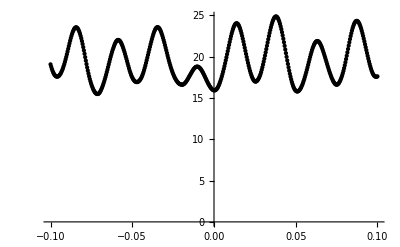

```mathematica
Show[gr13,Graphics[Point[volume]]]
```

```mathematica
Show[gr132,Graphics[Point[volume2]]]
```

Show::gcomb: Could not combine the graphics objects in Show[gr132,].

Show[gr132,-Graphics-]

```mathematica
gr132 = gr13;
volume2 = volume
```

{{-0.1,19.0669251295051261},{-0.0996,18.782681996279134},{-0.0992,18.5248543433305812},{-0.0988,18.2964287635207086},{-0.0984,18.0980426462403585},{-0.098,17.934278794514352},{-0.0976,17.8035162093012751},{-0.0972,17.704666798360595},{-0.0968,17.6353179547300805},{-0.0964,17.5938487935278616},{-0.096,17.5791995958050613},{-0.0956,17.5907619992272331},{-0.0952,17.6283741382750314},{-0.0948,17.6919725409662405},{-0.0944,17.7814806636247518},{-0.094,17.8965795586942065},{-0.0936,18.0369032393106181},{-0.0932,18.2019684572939831},{-0.0928,18.3911146265532715},{-0.0924,18.6034258625082671},{-0.092,18.8377935185641228},{-0.0916,19.0930111007987122},{-0.0912,19.3676812330906607},{-0.0908,19.6598757201739183},{-0.0904,19.9667907761534949},{-0.09,20.2851580386676247},{-0.0896,20.6126762411814717},{-0.0892,20.946914619047007},{-0.0888,21.2834192540733582},{-0.0884,21.6144618688810546},{-0.088,21.9336159701120863},{-0.0876,22.2356479073612086},{-0.0872,22.5158665227063892},{-0.0868,22.7698961748109703},{-0.0864,22.993704167378592},{-0.086,23.1836162411361926},{-0.0856,23.3363718979817385},{-0.0852,23.4492179315352018},{-0.0848,23.5199013191700495},{-0.0844,23.5468514227618648},{-0.084,23.5291277263872303},{-0.0836,23.4664726919047872},{-0.0832,23.3593538225784663},{-0.0828,23.2088458785724185},{-0.0824,23.016713329082247},{-0.082,22.7852593899172717},{-0.0816,22.5173135025673048},{-0.0812,22.2161695130244219},{-0.0808,21.885458030012714},{-0.0804,21.5291488408105529},{-0.08,21.1514144943714904},{-0.0796,20.7566273485484913},{-0.0792,20.349304372417091},{-0.0788,19.9340274479386572},{-0.0784,19.5155210169963773},{-0.078,19.0990969650434828},{-0.0776,18.6953934301412836},{-0.0772,18.3169443716387939},{-0.0768,17.9581284656694891},{-0.0764,17.6200823721732363},{-0.076,17.3049785764260271},{-0.0756,17.0147864435234162},{-0.0752,16.7503410604617962},{-0.0748,16.5105576397971561},{-0.0744,16.294699430611967},{-0.074,16.1027236918432131},{-0.0736,15.9343635349188499},{-0.0732,15.7899859641492828},{-0.0728,15.6705173629794174},{-0.0724,15.5778851501780125},{-0.072,15.5140004417962629},{-0.0716,15.4793521414943314},{-0.0712,15.473266060721329},{-0.0708,15.495198381862485},{-0.0704,15.5471747624546044},{-0.07,15.6415154598402495},{-0.0696,15.7721111347412322},{-0.0692,15.9265055372706161},{-0.0688,16.1020128270510377},{-0.0684,16.2973250415151512},{-0.068,16.5112115154652521},{-0.0676,16.7424906073317246},{-0.0672,16.9900410466259686},{-0.0668,17.2527635964303876},{-0.0664,17.5294828016130033},{-0.066,17.8183334431231835},{-0.0656,18.1172449574957533},{-0.0652,18.4246753622349466},{-0.0648,18.7391022004154593},{-0.0644,19.0571911256133788},{-0.064,19.373897189961319},{-0.0636,19.6847765032927988},{-0.0632,19.9864455626204212},{-0.0628,20.2756358955866425},{-0.0624,20.5492878887980588},{-0.062,20.804659879858928},{-0.0616,21.0403996290513469},{-0.0612,21.2596731529952123},{-0.0608,21.4672473522866518},{-0.0604,21.6482773528820864},{-0.06,21.7958484999100079},{-0.0596,21.9074579778808634},{-0.0592,21.9817246526080332},{-0.0588,22.0180575257471105},{-0.0584,22.0165316381891962},{-0.058,21.9779546599726814},{-0.0576,21.9038545670962606},{-0.0572,21.7961785646799058},{-0.0568,21.656903769371052},{-0.0564,21.4883137894137377},{-0.056,21.2930216568240205},{-0.0556,21.0740608402784879},{-0.0552,20.8349557404461585},{-0.0548,20.5790429787190732},{-0.0544,20.3094877843655972},{-0.054,20.0294291338432764},{-0.0536,19.7420949211430461},{-0.0532,19.4507405424913813},{-0.0528,19.158645681311743},{-0.0524,18.8691953250440427},{-0.052,18.58610347509428},{-0.0516,18.3148095225619834},{-0.0512,18.0662790789703038},{-0.0508,17.843839540014887},{-0.0504,17.6451666883818881},{-0.05,17.4700150028560337},{-0.0496,17.3192299001393408},{-0.0492,17.1933154488842241},{-0.0488,17.0922381782403896},{-0.0484,17.0147772609220915},{-0.048,16.9602029312159495},{-0.0476,16.9282235388180453},{-0.0472,16.9187653944661065},{-0.0468,16.9317913641145381},{-0.0464,16.9669785847721109},{-0.046,17.0239589198445884},{-0.0456,17.1025913853400873},{-0.0452,17.2030854495261529},{-0.0448,17.3260753533624197},{-0.0444,17.4731099501242433},{-0.044,17.6476065735898757},{-0.0436,17.8524855102284832},{-0.0432,18.0882106865108092},{-0.0428,18.3492487507146045},{-0.0424,18.629725219762765},{-0.042,18.9256151673853452},{-0.0416,19.2336764550634953},{-0.0412,19.5510477241778666},{-0.0408,19.8749152637522961},{-0.0404,20.2024269156234269},{-0.04,20.5306551533057977},{-0.0396,20.8566874453658393},{-0.0392,21.1779495903443014},{-0.0388,21.4959088431525913},{-0.0384,21.8042291407683386},{-0.038,22.101329960817278},{-0.0376,22.3899228256753027},{-0.0372,22.6586837043097233},{-0.0368,22.8989856705242438},{-0.0364,23.1067026331086929},{-0.036,23.2785460450238588},{-0.0356,23.4119358092373027},{-0.0352,23.5049074391639721},{-0.0348,23.5561268833145086},{-0.0344,23.5648945793895166},{-0.034,23.5312613775814263},{-0.0336,23.4559219004684252},{-0.0332,23.3407708818062396},{-0.0328,23.1882100867919654},{-0.0324,23.000461856142163},{-0.032,22.7811933140274086},{-0.0316,22.5364547096148762},{-0.0312,22.2744094477572361},{-0.0308,21.9968129158101817},{-0.0304,21.7044509613285719},{-0.03,21.4002390759906938},{-0.0296,21.0873378125985092},{-0.0292,20.7691197899119722},{-0.0288,20.4493337389130261},{-0.0284,20.1321849942667051},{-0.028,19.8222521489197838},{-0.0276,19.5241742248228611},{-0.0272,19.2374379218520204},{-0.0268,18.9628186525011806},{-0.0264,18.7017176443645816},{-0.026,18.4552769940696386},{-0.0256,18.2242913978610872},{-0.0252,18.0090816276096781},{-0.0248,17.809738782794259},{-0.0244,17.6262234285557931},{-0.024,17.4583902318711282},{-0.0236,17.3061005733297932},{-0.0232,17.1692814069422504},{-0.0228,17.0478232889452421},{-0.0224,16.9416316594756005},{-0.022,16.8505889404832523},{-0.0216,16.7745605962925737},{-0.0212,16.7131214205586467},{-0.0208,16.6664596312596878},{-0.0204,16.633601040229518},{-0.02,16.6132135657529538},{-0.0196,16.6050193166674305},{-0.0192,16.6100489860579081},{-0.0188,16.6336425592144792},{-0.0184,16.6818648361583826},{-0.018,16.7525129980470702},{-0.0176,16.8373703940061219},{-0.0172,16.9342451614996428},{-0.0168,17.044557925809908},{-0.0164,17.1683020686128849},{-0.016,17.3015597891964426},{-0.0156,17.4397274592991813},{-0.0152,17.5815141950373963},{-0.0148,17.7221563549131069},{-0.0144,17.8590851011938838},{-0.014,17.9915931984942965},{-0.0136,18.1317588781226213},{-0.0132,18.2694647092943932},{-0.0128,18.3951620209183666},{-0.0124,18.5063025807069721},{-0.012,18.6010921556230358},{-0.0116,18.6780079038618503},{-0.0112,18.7358023361738724},{-0.0108,18.7735337272492053},{-0.0104,18.7905763419143064},{-0.01,18.7866375447101035},{-0.0096,18.7617825978298178},{-0.0092,18.7164140929593224},{-0.0088,18.651256982017788},{-0.0084,18.567354774181144},{-0.008,18.4660319890778304},{-0.0076,18.3488477147658706},{-0.0072,18.217565501339589},{-0.0068,18.07411810922817},{-0.0064,17.9205619512614831},{-0.006,17.7590501097793378},{-0.0056,17.5918032096159251},{-0.0052,17.42111743868033},{-0.0048,17.2494744348999873},{-0.0044,17.0793488334222694},{-0.004,16.9181520137350638},{-0.0036,16.7649442931262236},{-0.0032,16.6185649473335708},{-0.0028,16.4807092685387069},{-0.0024,16.3531219439221403},{-0.002,16.237689956957599},{-0.0016,16.1372536581785901},{-0.0012,16.0550967622372518},{-0.0008,15.9924241073802289},{-0.0004,15.9477973404394273},{0.,15.9215156023251385},{0.0004,15.9154687087088291},{0.0008,15.9388539869664783},{0.0012,15.9917653381509837},{0.0016,16.0670053583378447},{0.002,16.1679400895522321},{0.0024,16.3009777047121673},{0.0028,16.4649349058794634},{0.0032,16.6542990773599975},{0.0036,16.8648842071085738},{0.004,17.0951652738684068},{0.0044,17.3444031198965583},{0.0048,17.6120030911539622},{0.0052,17.8974056509433694},{0.0056,18.1998964024490135},{0.006,18.5183455446240721},{0.0064,18.8512258906856225},{0.0068,19.1966649506378282},{0.0072,19.552522050115325},{0.0076,19.9166636668271337},{0.008,20.2871963298481468},{0.0084,20.6617353311867831},{0.0088,21.0371200567355174},{0.0092,21.4096430367299924},{0.0096,21.7750657674789458},{0.01,22.1287080426312137},{0.0104,22.465417005827792},{0.0108,22.7803333667151655},{0.0112,23.0689554753673995},{0.0116,23.3270690242655867},{0.012,23.5505073460521146},{0.0124,23.735394404725394},{0.0128,23.8784067584475785},{0.0132,23.9768993997766842},{0.0136,24.0289682702078729},{0.014,24.0335042109864183},{0.0144,23.9902666091425658},{0.0148,23.8999061287613337},{0.0152,23.7639480594026331},{0.0156,23.584774165687989},{0.016,23.365588375631404},{0.0164,23.1103545469764846},{0.0168,22.8236385088571545},{0.0172,22.5099071795371657},{0.0176,22.1737911810885215},{0.018,21.8202829122698709},{0.0184,21.4545040979114425},{0.0188,21.0810750282934265},{0.0192,20.7042073014430663},{0.0196,20.3279781548313068},{0.02,19.9563296411224123},{0.0204,19.5929924586976298},{0.0208,19.2415439199998772},{0.0212,18.9054398583492826},{0.0216,18.5878999871251907},{0.022,18.2919814272581469},{0.0224,18.0205795545469805},{0.0228,17.7763470156579331},{0.0232,17.5615135742755264},{0.0236,17.3779546412591195},{0.024,17.2273247068027793},{0.0244,17.110909820914511},{0.0248,17.0300044402071826},{0.0252,16.9864072327087321},{0.0256,16.9824602130670606},{0.026,17.0188436617009167},{0.0264,17.0880527764565677},{0.0268,17.1861637042711095},{0.0272,17.3109569715870357},{0.0276,17.4622430193544282},{0.028,17.6425899088658973},{0.0284,17.8546550151599028},{0.0288,18.1148258995602625},{0.0292,18.4049050282535305},{0.0296,18.7162521274406721},{0.03,19.0469712320057205},{0.0304,19.3944204897618384},{0.0308,19.7563656312065135},{0.0312,20.1311234624656699},{0.0316,20.5173087307176019},{0.032,20.9132757711201336},{0.0324,21.3139464243136416},{0.0328,21.7137189689002952},{0.0332,22.1078796539590847},{0.0336,22.4919573418410685},{0.034,22.86152340848545},{0.0344,23.212140674784596},{0.0348,23.5394134878615198},{0.0352,23.8390159013106491},{0.0356,24.1068623737195509},{0.036,24.3391340032412309},{0.0364,24.5323940773726612},{0.0368,24.6836046414846386},{0.0372,24.7902088869755204},{0.0376,24.8502748818997326},{0.038,24.8624794494939572},{0.0384,24.8262878733562609},{0.0388,24.7418704880121645},{0.0392,24.6101169500501094},{0.0396,24.4326548407969462},{0.04,24.2116931239393693},{0.0404,23.9500931006691467},{0.0408,23.6511890208661804},{0.0412,23.3187608334392529},{0.0416,22.9569457033136928},{0.042,22.5701069491927022},{0.0424,22.1627993205628826},{0.0428,21.7396670532918854},{0.0432,21.3054408051005844},{0.0436,20.8644949390878445},{0.044,20.4210247046043776},{0.0444,19.9792210427628767},{0.0448,19.5432202734761518},{0.0452,19.117008772615975},{0.0456,18.7041987873511353},{0.046,18.3079670483183996},{0.0464,17.9315083937480999},{0.0468,17.5781720416555949},{0.0472,17.2508449314418151},{0.0476,16.9525328162740863},{0.048,16.6857666749088587},{0.0484,16.4521541050320224},{0.0488,16.2532342276072335},{0.0492,16.0894783225618525},{0.0496,15.9613672353692238},{0.05,15.8689735481722707},{0.0504,15.8107109360711977},{0.0508,15.7849160704082934},{0.0512,15.7901339596928754},{0.0516,15.8249514790993526},{0.052,15.8878810190917275},{0.0524,15.9775332957036031},{0.0528,16.0930756212241555},{0.0532,16.2338435049954306},{0.0536,16.3988556737464677},{0.054,16.5869706893865505},{0.0544,16.7962945183148982},{0.0548,17.0249077099145723},{0.0552,17.2710737536517449},{0.0556,17.5330348794596631},{0.056,17.8090085974562733},{0.0564,18.0972197620924717},{0.0568,18.3955383129255488},{0.0572,18.7028189705236123},{0.0576,19.0171334725881813},{0.058,19.3341715566140842},{0.0584,19.6495373973274639},{0.0588,19.9586289195722699},{0.0592,20.2566865852571603},{0.0596,20.539537508012284},{0.06,20.8033926753805112},{0.0604,21.0447842489735741},{0.0608,21.2604996608209156},{0.0612,21.4476790481459254},{0.0616,21.6038673648266304},{0.062,21.7271345611202662},{0.0624,21.8164214683540543},{0.0628,21.8710349064317349},{0.0632,21.8899445663118577},{0.0636,21.8729991835229249},{0.064,21.8208156714811672},{0.0644,21.7343453537228157},{0.0648,21.615047350054553},{0.0652,21.4651338975585837},{0.0656,21.2922241820194991},{0.066,21.0947902357413568},{0.0664,20.8758959619472932},{0.0668,20.639572849282473},{0.0672,20.3930102833702911},{0.0676,20.1426236833348717},{0.068,19.8860512035637669},{0.0684,19.6241427292206261},{0.0688,19.3594736156065181},{0.0692,19.0947706113026996},{0.0696,18.8325173189522559},{0.07,18.5750858653230324},{0.0704,18.3247323179643153},{0.0708,18.0836766619712073},{0.0712,17.854016020842078},{0.0716,17.6377295752552179},{0.072,17.4366376695479097},{0.0724,17.2524241945291017},{0.0728,17.0867221402738565},{0.0732,16.9412086325195226},{0.0736,16.8177795639163357},{0.074,16.7187577198574111},{0.0744,16.64780482927004},{0.0748,16.6091970436650982},{0.0752,16.6049860735706609},{0.0756,16.6366955580074851},{0.076,16.7045360702642221},{0.0764,16.8059441955961368},{0.0768,16.9372700748078664},{0.0772,17.096021584471135},{0.0776,17.2810462024120746},{0.078,17.4918556126934135},{0.0784,17.7287554571260841},{0.0788,17.9930252082664808},{0.0792,18.2856310369753281},{0.0796,18.6050816241109054},{0.08,18.9496168687549726},{0.0804,19.3178779753021672},{0.0808,19.7059646224496703},{0.0812,20.1069630362927541},{0.0816,20.5151141068439884},{0.082,20.9253479793321873},{0.0824,21.3327549738834641},{0.0828,21.7324275328654046},{0.0832,22.1193561290133545},{0.0836,22.4885945624663037},{0.084,22.8352989154190915},{0.0844,23.1547924240815952},{0.0848,23.442779261303226},{0.0852,23.6953146617094497},{0.0856,23.9090228139330314},{0.086,24.0810275230121107},{0.0864,24.2092105328238851},{0.0868,24.2920869833639124},{0.0872,24.3288763080663131},{0.0876,24.3195222909734206},{0.088,24.2653213011326017},{0.0884,24.1685516203087936},{0.0888,24.0315863690722829},{0.0892,23.8567392282793485},{0.0896,23.645956971849472},{0.09,23.4019397189954646},{0.0904,23.1284881219973215},{0.0908,22.8303024237985568},{0.0912,22.5129026490920552},{0.0916,22.1817379185210051},{0.092,21.840341057718458},{0.0924,21.4917524810814236},{0.0928,21.1391796037014075},{0.0932,20.78586406598561},{0.0936,20.4350972537187943},{0.094,20.090166521143761},{0.0944,19.7541136205329124},{0.0948,19.4298927390114251},{0.0952,19.120418726821061},{0.0956,18.8287260255273559},{0.096,18.5581960975846698},{0.0964,18.3131029053940289},{0.0968,18.1003952378980415},{0.0972,17.9260736824872602},{0.0976,17.7883409275173001},{0.098,17.6875946957624954},{0.0984,17.6167473273922646},{0.0988,17.5746132570277425},{0.0992,17.5600206804705969},{0.0996,17.5720500883262574},{0.1,17.6099068698251458}}

```mathematica
Speak["He acabado"]
```

```mathematica
Print[λ//MatrixForm]
```

(5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5)

```mathematica
Print[γ//MatrixForm]
```

(2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2)